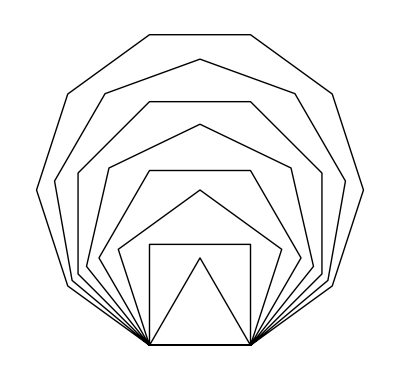

```mathematica
Graphics@Line@AnglePath[Flatten[Table[360°/#,{#}]&/@Range@10]]
```

```mathematica
Flatten[Table[360°/#,{#}]&/@Range@10]
```

{360 °,180 °,180 °,120 °,120 °,120 °,90 °,90 °,90 °,90 °,72 °,72 °,72 °,72 °,72 °,60 °,60 °,60 °,60 °,60 °,60 °,(360 °)/7,(360 °)/7,(360 °)/7,(360 °)/7,(360 °)/7,(360 °)/7,(360 °)/7,45 °,45 °,45 °,45 °,45 °,45 °,45 °,45 °,40 °,40 °,40 °,40 °,40 °,40 °,40 °,40 °,40 °,36 °,36 °,36 °,36 °,36 °,36 °,36 °,36 °,36 °,36 °}

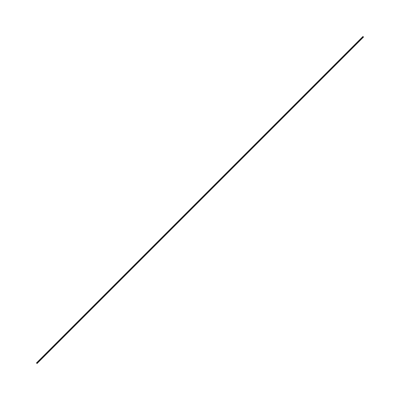

```mathematica
Graphics[Line[{{0,0},{1,1}}]]
```

```mathematica
AnglePath[{90°,90°,90°}]
```

{{0,0},{0,1},{-1,1},{-1,0}}

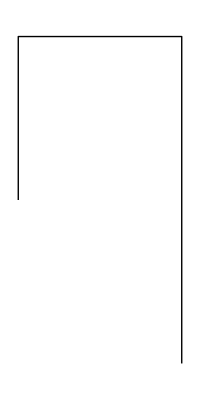

```mathematica
Graphics[Line@AnglePath[{{2,90°},{1,90°},{1,90°}}]]
```

```mathematica
ConstantArray[1,3]
```

{1,1,1}

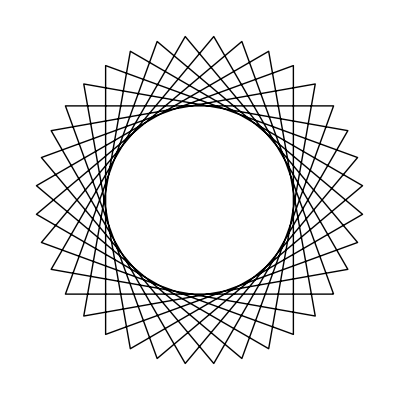

```mathematica
Graphics[Line[AnglePath[ConstantArray[110°,36]]]]
```

```mathematica
AnglePath[ConstantArray[110°,1]]
```

{{0,0},{-Sin[20 °],Cos[20 °]}}

```mathematica
LCM[110,360]
```

3960

```mathematica
%/110
```

36

```mathematica
Clear[n];
Manipulate[Graphics@Line@AnglePath[Flatten[Table[360°/#,{#}]&/@Range@n]],{n,10}]
```

```mathematica
f[n_]:=180*(n-2)
```

```mathematica
f[3]
```

180

```mathematica
f[4]
```

360

```mathematica
f[5]
```

540

```mathematica
540/5
```

108

```mathematica
180-2*72
```

36

```mathematica
180-36
```

144

```mathematica
Manipulate[Graphics@Line@AnglePath@ConstantArray[-144°,n],{n,1,5,1}]
```

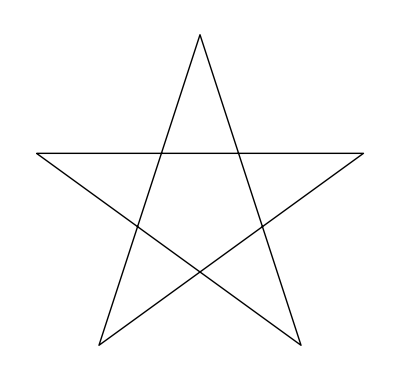

```mathematica
Graphics@Line@AnglePath@Table[{-72°,144°},5]
```

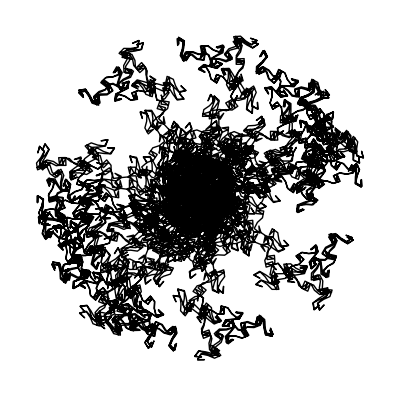

```mathematica
Graphics@Line@AnglePath@N@Range[10000]
```

```mathematica
AnglePath@N@Range[3]
```

{{0.,0.},{0.540302,0.841471},{-0.44969,0.982591},{0.51048,0.703175}}

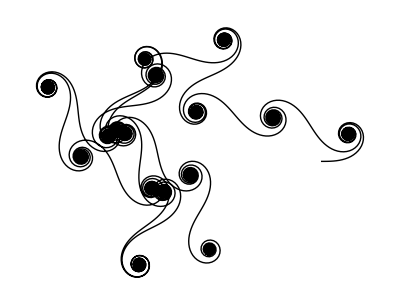

```mathematica
Graphics@Line@AnglePath@N@Range[0,100,0.01]
```

```mathematica
Rotate[Graphics[BSplineCurve[Map[AnglePath[Transpose[{0.65^Range[11],#}]]&, Tuples[{-Pi/3, Pi/8},11]]]],Pi/2]
```

-Graphics-

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
Export["test.jpg",-Graphics-]
```

test.jpg

```mathematica
Play[Sin[440 2 Pi t],{t,0,1}]
```

-Graphics-

```mathematica
Play[NotebookWrite]
```

```mathematica
NKS
```

NKS

```mathematica
Remove[NKS]
```